```mathematica
Manipulate[Plot[{1-ⅇ^(-2n(gy-y)(gx-x)),
If[y >-(1-2 gx gy n+2 gy n x)/(2 gx n-2 n x),2n(gy-y)(gx-x),1],
If[y>gy - π/(4 n (gx-x)),Cos[2 n (gx-x)(y-(gy - π/(4 n (gx-x)))) ],1],
If[y>-(-2 gx^2 n^2+gx^3 gy n^3+4 gx n^2 x-3 gx^2 gy n^3 x-2 n^2 x^2+3 gx gy n^3 x^2-gy n^3 x^3)/(-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3)-(2^(1/3) (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4))/(3 (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3)/(3 2^(1/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3)),(-2 (gx n-n x) (-gy+y)-2/15 (gx^3 n^3-3 gx^2 n^3 x+3 gx n^3 x^2-n^3 x^3) (-gy+y)^3)/(1+(-gx n+n x) (-gy+y)+2/5 (gx^2 n^2-2 gx n^2 x+n^2 x^2) (-gy+y)^2+1/15 (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (-gy+y)^3),1]}
,{y,-1,gy}, PlotRange->Full],{n,1,40},{x,-3,gx},{gy,0.5,2},{gx,0.5,2}]
```

Trig Approximation. f[y] = Cos[b(y-y0)]. f[g_y] = Cos[b(g_y-y0)] = 0, so b(g_y-y0) = π/2. f’[y]=-b Sin[b(y-y0)]. f’[g] = -b Sin[b(g-y0)] = -b Sin[π/2] = -b = -2 n (g_x - x). b = 2n(g_x -x)

```mathematica
Evaluate[PadeApproximant[1-ⅇ^(-2n(gy-y)(gx-x)),{y,gy,{3,3}}]]
```

(-2 (gx n-n x) (-gy+y)-2/15 (gx^3 n^3-3 gx^2 n^3 x+3 gx n^3 x^2-n^3 x^3) (-gy+y)^3)/(1+(-gx n+n x) (-gy+y)+2/5 (gx^2 n^2-2 gx n^2 x+n^2 x^2) (-gy+y)^2+1/15 (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (-gy+y)^3)

```mathematica
Solve[(-2 (gx n-n x) (-gy+y)-2/15 (gx^3 n^3-3 gx^2 n^3 x+3 gx n^3 x^2-n^3 x^3) (-gy+y)^3)/(1+(-gx n+n x) (-gy+y)+2/5 (gx^2 n^2-2 gx n^2 x+n^2 x^2) (-gy+y)^2+1/15 (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (-gy+y)^3) == 1, y]
```

{{y→-(-2 gx^2 n^2+gx^3 gy n^3+4 gx n^2 x-3 gx^2 gy n^3 x-2 n^2 x^2+3 gx gy n^3 x^2-gy n^3 x^3)/(-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3)-(2^(1/3) (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4))/(3 (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3)/(3 2^(1/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3))},{y→-(-2 gx^2 n^2+gx^3 gy n^3+4 gx n^2 x-3 gx^2 gy n^3 x-2 n^2 x^2+3 gx gy n^3 x^2-gy n^3 x^3)/(-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3)+((1+ⅈ √3) (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4))/(3 2^(2/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))-((1-ⅈ √3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))/(6 2^(1/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3))},{y→-(-2 gx^2 n^2+gx^3 gy n^3+4 gx n^2 x-3 gx^2 gy n^3 x-2 n^2 x^2+3 gx gy n^3 x^2-gy n^3 x^3)/(-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3)+((1-ⅈ √3) (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4))/(3 2^(2/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))-((1+ⅈ √3) (27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6+√(4 (9 gx^4 n^4-36 gx^3 n^4 x+54 gx^2 n^4 x^2-36 gx n^4 x^3+9 n^4 x^4)^3+(27 gx^6 n^6-162 gx^5 n^6 x+405 gx^4 n^6 x^2-540 gx^3 n^6 x^3+405 gx^2 n^6 x^4-162 gx n^6 x^5+27 n^6 x^6)^2))^(1/3))/(6 2^(1/3) (-gx^3 n^3+3 gx^2 n^3 x-3 gx n^3 x^2+n^3 x^3))}}

```mathematica
Sin[π/2]
```

1

```mathematica
ⅇ^-x//ExpToTrig
```

Cosh[x]-Sinh[x]

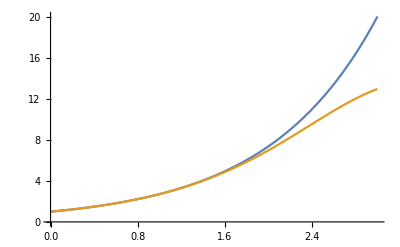

```mathematica
Plot[{ⅇ^x, (12+6 x+x^2)/(12-6 x+x^2)},{x,0,3}]
```

```mathematica
PadeApproximant[1-ⅇ^(-2n(gy-y)(gx-x)),{y,gy,{2,2}}]//Simplify
```

-(2 n (gx-x) (-gy+y))/(1+n (gx-x) (gy-y)+1/3 n^2 (gx-x)^2 (gy-y)^2)

```mathematica
Denominator[(-19+8 x-x^2+ⅇ (7+4 x+x^2))/(ⅇ (7+4 x+x^2))]
```

ⅇ (7+4 x+x^2)

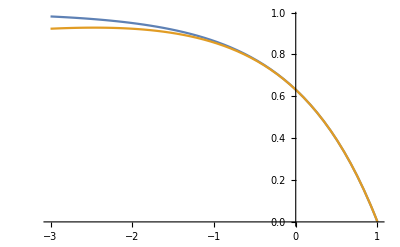

```mathematica
Plot[{1-Exp[-(1-x)],-(6 n (-1+x))/(3-3 n (-1+x)+n^2 (-1+x)^2)},{x,-3,1}]
```

```mathematica
PadeApproximant[Exp[x],{x,0,{2,2}}]//Simplify
```

(12+6 x+x^2)/(12-6 x+x^2)

```mathematica
D[1-ⅇ^(-2 n a x),{x}]
```

2 a ⅇ^(-2 a n x) n

```mathematica
Solve[2n(gy-y)(gx-x) ==1 ,y]//Simplify
```

{{y→-(1-2 gx gy n+2 gy n x)/(2 gx n-2 n x)}}